# MATH2100 Assignment 1

Michael Kasumagic, 44302669

## Question 1

### (a)

```mathematica
f[x_]:=x-3+Exp[2x]
h[x_]:=x^4+2x^3+x+1
```

```mathematica
N[h[2]-f[4],6]
```

-2946.96

```mathematica
h[f[x]]-f[h[x]]
```

ⅇ^(2 x)-ⅇ^(2 (1+x+2 x^3+x^4))-2 x^3-x^4+2 (-3+ⅇ^(2 x)+x)^3+(-3+ⅇ^(2 x)+x)^4

### (b)

```mathematica
dist[x_,y_]:=Sqrt[(3-x)^2+(4-y)^2]
dist[-3,5]
```

√37

### (c)

```mathematica
sol1c=Solve[{w+x+y+z==4,w+2x+3y+4z==5,2w+x-y-2z==0},{x,y,z}]
```

{{x→-3-w,y→17-w,z→-10+w}}

```mathematica
sol1c/.w->0
sol1c/.w->1
sol1c/.w->-1
```

{{x→-3,y→17,z→-10}}

{{x→-4,y→16,z→-9}}

{{x→-2,y→18,z→-11}}

### (d)

#### (i)

```mathematica
p[x_]:=-x^4+2x^3-5x^2+4x+1
```

#### (ii)

```mathematica
Solve[{p[x]==0},{x}]
```

{{x→1/2 (1-√(-7+4 √5))},{x→1/2 (1+√(-7+4 √5))},{x→1/2 (1-ⅈ √(7+4 √5))},{x→1/2 (1+ⅈ √(7+4 √5))}}

```mathematica
NSolve[{p[x]==0},{x}]
```

{{x→-0.197186},{x→0.5-1.99651 ⅈ},{x→0.5+1.99651 ⅈ},{x→1.19719}}

#### (iii)

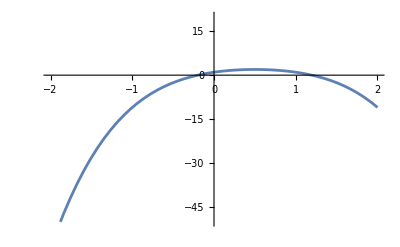

```mathematica
Plot[p[x],{x,-2,2},PlotRange->{-50,20}]
```

#### (iv)

```mathematica
p'[x]
```

4-10 x+6 x^2-4 x^3

```mathematica
NSolve[{p'[x]==0},{x}]
```

{{x→0.5},{x→0.5-1.32288 ⅈ},{x→0.5+1.32288 ⅈ}}

#### (v)

```mathematica
NumberForm[NIntegrate[p[x],{x,-1,1}],3]
```

-1.73

#### (vi)

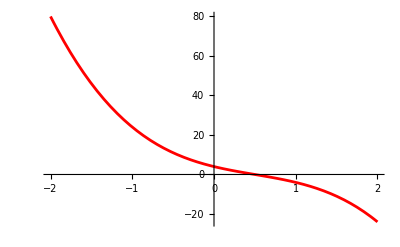

```mathematica
Plot[p'[x],{x,-2,2},PlotStyle->Red]
```

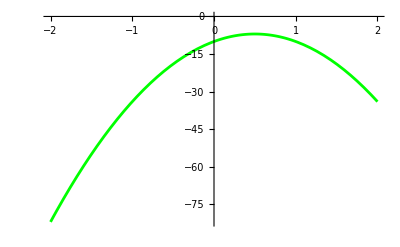

```mathematica
Plot[p''[x],{x,-2,2},PlotStyle->Green]
```

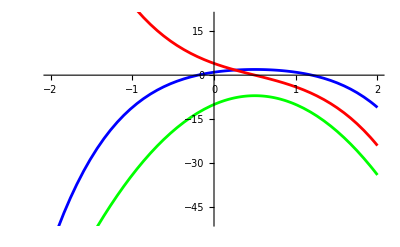

```mathematica
Show[
Plot[p[x],{x,-2,2},PlotStyle->Blue],
Plot[p'[x],{x,-2,2},PlotStyle->Red],
Plot[p''[x],{x,-2,2},PlotStyle->Green],
PlotRange->{-50,20}
]
```

## Question 3

```mathematica
ClearAll["global"]
```

### (b)

```mathematica
ivp3b={y'[x]==-2y[x]+4Cos[2x],y[Pi/4]==1};
sol3b=DSolve[ivp3b,y[x],x]
```

{{y[x]→Cos[2 x]+Sin[2 x]}}

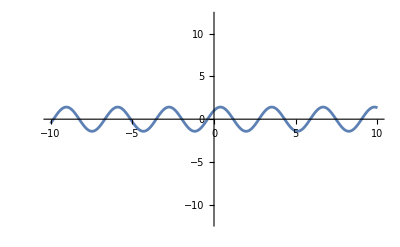

```mathematica
Plot[y[x]/.sol3b,{x,-10,10},PlotRange->{-12,12}]
```

### (c)

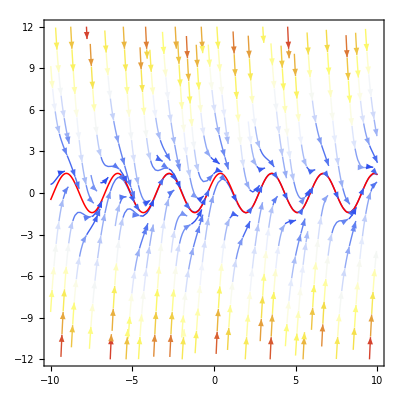

```mathematica
Show[
StreamPlot[{1,-2y+4Cos[2x]},{x,-10,10},{y,-12,12},StreamColorFunction->"TemperatureMap"],
Plot[y[x]/.sol3b,{x,-10,10},PlotStyle->{AbsoluteThickness[1.1],Red}]
]
```